```mathematica
Clear["Global`*"];
```

```mathematica
cmpToPt[z_]:={Re[z],Im[z]}
initCord[{a_,b_,c_,d_}]:={0,-1/a-1/b,-1/a+(a-b)/(a+b)/c+I*(a+b+c-d)/(a+b)/c,-1/a+(a-b)/(a+b)/d-I*(a+b+d-c)/(a+b)/d}
expand4[{v1_,v2_,v3_,v4_}]:={{v2,v3,v4,2*(v2+v3+v4)-v1},{v1,v3,v4,2*(v1+v3+v4)-v2},{v1,v2,v4,2*(v1+v2+v4)-v3},{v1,v2,v3,2*(v1+v2+v3)-v4}}
expand3[{v1_,v2_,v3_,v4_}]:={{v2,v3,v4,2*(v2+v3+v4)-v1},{v1,v3,v4,2*(v1+v3+v4)-v2},{v1,v2,v4,2*(v1+v2+v4)-v3}}
```

```mathematica
pairToCirc[c_,z_]:=If[c<0,
{Thick,GrayLevel[0.2],Circle[cmpToPt[z],1/Abs[c]]},
{Thin,GrayLevel[0.2],Circle[cmpToPt[z],1/Abs[c]]}]
pairToCircDot[c_,z_]:=If[c<0,
{Thick,GrayLevel[0.2],Circle[cmpToPt[z],1/Abs[c]],PointSize[Large],Orange,Point[cmpToPt[z]]},
{Thin,GrayLevel[0.5],Circle[cmpToPt[z],1/Abs[c]],PointSize[Large],Orange,Point[cmpToPt[z]]}]
pairToCircNew[c_,z_]:={Thin,EdgeForm[Orange],LightOrange,Disk[cmpToPt[z],1/Abs[c]]}
pairToText[c_,z_,cmax_]:=If[c<0,
{Text[Style[c,30,FontFamily->"Times New Roman",LightGray,Bold],cmpToPt[z]+{0.8/c,0.8/c}]},
{Text[Style[c,If[c/Abs[cmax]<50,c,""],200*Abs[cmax]/c,FontFamily->"Times New Roman",LightGray,Bold],cmpToPt[z]]}]
```

```mathematica
cinit={-6,11,14,15};
zinit=initCord[cinit];
```

```mathematica
vc1=cinit;vcz1=cinit*zinit;
vc2=expand4[vc1];vcz2=expand4[vcz1];
vz2=vcz2/vc2;
vc3=expand3/@vc2//Flatten[#,1]&;vcz3=expand3/@vcz2//Flatten[#,1]&;
vz3=vcz3/vc3;
vc4=expand3/@vc3//Flatten[#,1]&;vcz4=expand3/@vcz3//Flatten[#,1]&;
vz4=vcz4/vc4;
```

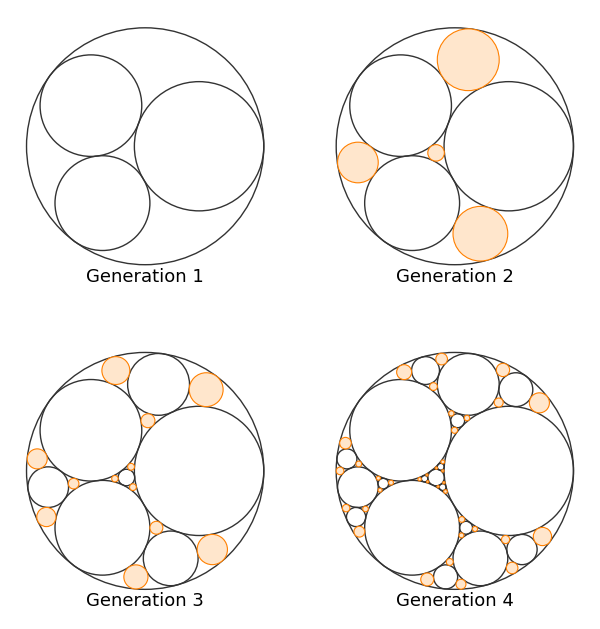

```mathematica
ggen1=Graphics[{
Table[pairToCirc[cinit[[k]],zinit[[k]]],{k,4}],
Text[Style["Generation 1",18,FontFamily->"Times New Roman"],{0,1.1/cinit[[1]]}]
}];
ggen2=Graphics[{
Table[pairToCirc[cinit[[k]],zinit[[k]]],{k,4}],
Table[pairToCircNew[vc2[[k,4]],vz2[[k,4]]],{k,Length[vc2]}],
Text[Style["Generation 2",18,FontFamily->"Times New Roman"],{0,1.1/cinit[[1]]}]
}];
ggen3=Graphics[{
Table[pairToCirc[cinit[[k]],zinit[[k]]],{k,4}],
Table[pairToCirc[vc2[[k,4]],vz2[[k,4]]],{k,Length[vc2]}],
Table[pairToCircNew[vc3[[k,4]],vz3[[k,4]]],{k,Length[vc3]}],
Text[Style["Generation 3",18,FontFamily->"Times New Roman"],{0,1.1/cinit[[1]]}]
}];
ggen4=Graphics[{
Table[pairToCirc[cinit[[k]],zinit[[k]]],{k,4}],
Table[pairToCirc[vc2[[k,4]],vz2[[k,4]]],{k,Length[vc2]}],
Table[pairToCirc[vc3[[k,4]],vz3[[k,4]]],{k,Length[vc3]}],
Table[pairToCircNew[vc4[[k,4]],vz4[[k,4]]],{k,Length[vc4]}],
Text[Style["Generation 4",18,FontFamily->"Times New Roman"],{0,1.1/cinit[[1]]}]
}];
GraphicsGrid[{{ggen1,ggen2},{ggen3,ggen4}},ImageSize->600]
```

```mathematica
pthull2=cmpToPt/@{zinit[[2]],vz2[[4,4]],zinit[[3]],vz2[[2,4]],zinit[[4]],vz2[[3,4]]};
pthull3=cmpToPt/@{vz3[[12,4]],vz3[[11,4]],vz3[[6,4]],vz3[[5,4]],vz3[[8,4]],vz3[[9,4]]};
```

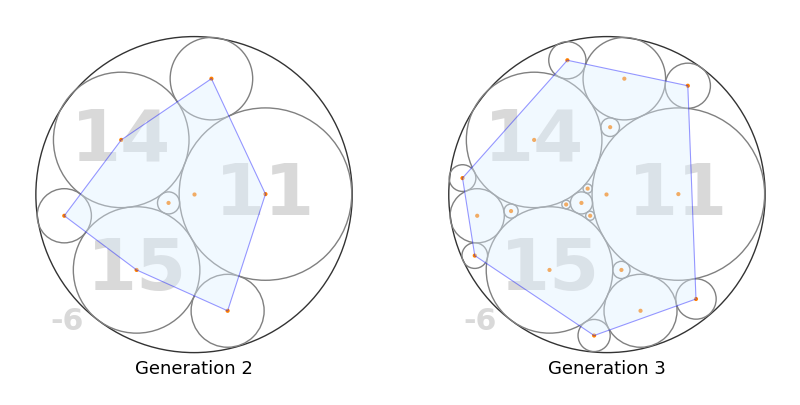

```mathematica
ghull2=Graphics[{
Table[pairToCircDot[cinit[[k]],zinit[[k]]],{k,4}],
 Table[pairToText[cinit[[k]],zinit[[k]],cinit[[1]]],{k,4}],
Table[pairToCircDot[vc2[[k,4]],vz2[[k,4]]],{k,Length[vc2]}],
{Opacity[0.4],EdgeForm[{Thick,Blue}],LightBlue,Polygon[pthull2]},
Text[Style["Generation 2",18,FontFamily->"Times New Roman"],{0,1.1/cinit[[1]]}]
}];
ghull3=Graphics[{
Table[pairToCircDot[cinit[[k]],zinit[[k]]],{k,4}],
 Table[pairToText[cinit[[k]],zinit[[k]],cinit[[1]]],{k,4}],
Table[pairToCircDot[vc2[[k,4]],vz2[[k,4]]],{k,Length[vc2]}],
Table[pairToCircDot[vc3[[k,4]],vz3[[k,4]]],{k,Length[vc3]}],
{Opacity[0.4],EdgeForm[{Thick,Blue}],LightBlue,Polygon[pthull3]},
Text[Style["Generation 3",18,FontFamily->"Times New Roman"],{0,1.1/cinit[[1]]}]
}];
GraphicsRow[{ghull2,ghull3},ImageSize->800]
```

```mathematica
areahull2=Area[ConvexHullMesh[pthull2]];
areahull2ideal=670/23023;
ratiohull2=areahull2*cinit[[1]]^2/Pi;
NumberForm[areahull2,16]
NumberForm[ratiohull2,16]
```

0.02910133344915954

0.3334767169679465

```mathematica
areahull3=Area[ConvexHullMesh[pthull3]];
areahull3ideal=45650065/866875849;
ratiohull3=areahull3*cinit[[1]]^2/Pi;
NumberForm[areahull3,16]
NumberForm[ratiohull3,16]
```

0.05266044157610393

0.6034442099212009